# Gyógyszeradagolási modell

Fülöp Zsolt
Vegyészmérnöki BSc

## Absztrakt

A rekeszrendszerek alkalmazása a gyógyszeradagolási modell segítségével. Egy adott gyógyszer felszívódásának folyamatát mutatom be a szervezet két “rekeszén” át. Az elemzést egy adott mennyiségű gyógyszer elfogyasztása esetén hajtom végre. Az esetek vizsgálata különböző egyénekre, akiknek eltérő a gyógyszer kirülülési sebessége. VIzsgálom továbbá az ólom kirülésének folyamatát a szervezetben, úgy ha a kiinduláskor nem, illetve ha van ólom a szervezetben.

## Bevezetés A rekeszrendszereket sok területen alkalmazhatjuk, ilyen például a kémia, ahol az anyagok egymásba átalakulását vizsgáljuk, vagy amikor valamilyen anyag élő szervezetbe jutását követjük nyomon. Emellett jól használható a populációdinamikában is, mikor egyedek vándorlását figyeljük meg adott területek között. Ezeknél az egyes állapotok a kompartmentek vagy rekeszek. A projektemben a gyógyszeradagolási modellen keresztül, illetve az ólom felszívódásán keresztül igyekszem bemutatni a rekeszrendszerek értelmét. A gyógyszeradagolási modellben a testet két rekeszre osztjuk fel amiből az egyik a vér, a másik az emésztőrendszer. Az ólom szervezetben való felszívódásást 3 rekeszen (vér, csontok és szövetek) keresztül vizsgálom.

## További fejezetek Gyógyszer kiürülésének folyamata a szervezetből A szervezetben a gyógyszer felszívódását az alábbi differenciálegyenlet írja le: x’[t]==-k1*x[t] y’[t]==k1*x[t]-k2*y[t] ahol az x(t), illetve y(t), hogy mennyi gyógyszer marad az emésztőtraktusban, illetve mennyi a gyógyszer mennyisége a vérben t idő elteltével. Tegyük fel, hogy az emésztőtraktusban kezdetben A egység gyógyszer van és feltételezzük, hogy a vizsgálat ideje alatt nem kerül újabb adag antihisztamin a szervezetbe. Tehát: x ’[t]==-k1*x[t], x[0]=A y’[t]==k1*x[t]-k2*y[t], y[0]=0

```mathematica
Oldjuk meg az egyenletet !
```

```mathematica
Clear[x,y]
eqns={x'[t]==-k1*x[t],y'[t]==k1*x[t]-k2*y[t],x[0]==A,y[0]==0};
sol=DSolve[eqns,{x,y},t]
```

```mathematica
Az y-ra kapott függvényt egyszerűsíthetjük!
```

```mathematica
Simplify[-(A ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1)/(k1-k2)]
```

```mathematica
Az anthisztamin esetében ismertek az együtthatók:
k1=0.6931,k2=0.0231
Így tehát:
```

```mathematica
Clear[eqns2]
Clear[sol2]
eqns2= {x'[t]==-0.6931*x[t],y'[t]==0.6931*x[t]-0.0231*y[t],x[0]==A,y[0]==0};
sol2= DSolve[eqns2,{x,y},t]
```

```mathematica
{{x->Function[{t},0.9999999999999999 A ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)+1.1485008632353674*^-16 ⅇ^(0.6931 t))],y->Function[{t},-1.0344776119402983 A ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)-1. ⅇ^(0.6931 t))]}}
```

```mathematica
Látható, hogy k2 sokkal kisebb a k1 értéknél,ezért az antihisztamin hosszabb ideig marad magasabb szinten a vérben,mint az emésztőtraktusban. Ezt bizonyítandó tegyük fel, hogy A=1.
```

```mathematica
Clear[eqns3]
Clear[sol3]
eqns3= {x'[t]==-0.6931*x[t],y'[t]==0.6931*x[t]-0.0231*y[t],x[0]==1,y[0]==0};
sol3= DSolve[eqns3,{x,y},t]
```

```mathematica
Mostmár ábrázolhatjuk a két megoldást:
```

```mathematica
Plot[0.9999999999999999 ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)+1.1485008632353674*^-16 ⅇ^(0.6931 t)),{t,0,6}]
```

```mathematica
Plot[-1.0344776119402983 ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)-1. ⅇ^(0.6931 t)),{t,0,6}]
```

```mathematica
Illetve közös koordinátarendszerben:
```

```mathematica
Plot[{0.9999999999999999 ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)+1.1485008632353674*^-16 ⅇ^(0.6931 t)),-1.0344776119402983 ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)-1. ⅇ^(0.6931 t))},{t,0,6}]
```

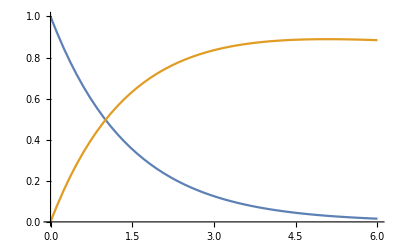

```mathematica
Persze, hosszútávon:
```

```mathematica
Plot[{0.9999999999999999 ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)+1.1485008632353674*^-16 ⅇ^(0.6931 t)),-1.0344776119402983 ⅇ^(-0.7162000000000001 t) (1. ⅇ^(0.0231 t)-1. ⅇ^(0.6931 t))},{t,0,100}]
```

```mathematica
Látható, hogy a vérből az antihisztamin sokkal lassabba ürül ki, mint az emésztőrendszerből.

Azonban k2,azaz a gyógyszer kiürülési sebességének együtthatója,nagyban függhet a gyógyszert bevevő egyén korától és egészségi állapotától. Pontosabban,egy idős és beteg
embernek sokkal több idő alatt ürül ki a szervezetéből az antihisztamin.Ábrázoljuk k2 különböző értékeire a vérben lévő antihisztamin szintjét egy 24 órás időintervallumon!
```

```mathematica
Clear[eqns4]
eqns4={x'[t]==-0.6931*x[t],y'[t]==0.6931*x[t]-k2*y[t],x[0]==A,y[0]==0};
Manipulate [Plot[-(1 ⅇ^(-0.6931 t-k2 t) (-ⅇ^(0.6931 t)+ⅇ^(k2 t)) 0.6931)/(0.6931-k2),{t,0,24}],{k2,0.00231,0.231}]
```

```mathematica
Következő példaként nézzük az ólom kiürülését a szervezetből, a folyamatot az alábbiak szerint kell elképzelni:
```

```mathematica
Az ólom ürülését a következő differenciálegyenlet-rendszer írja le:
```

```mathematica
x'[t]==I1+k12*y[t]+k13*k[t]-(k01+k21+k31)*x[t]
y'[t]==k21*x[t]-(k02+k12)y[t]
k'[t]==k31*x[t]-k13*k[t]

Vegyük az I1 értékét 49,3 µg/nap-nak míg  kji-t (nap)^-1 mértékegységben mérjük.
Irodalmi adatok szerint az együtthatók:
k01=0,0211,k21=0,0111,k31=0,0039;
	k02=0,0162,k12=0,0124,k13=0,000035;

Vizsgáljuk meg az egyenletrendszert úgy, ha a kezdeti időpontban nincsen ólom sem a szövetekben (x), csontokban (k)és a vérben(y).
```

```mathematica
Clear[x,y,I1,k12,k13,k,k01,k21,k31,k02,k31,t]
eqns5={x'[t]==I1+k12*y[t]+k13*k[t]-(k01+k21+k31)*x[t],y'[t]==k21*x[t]-(k02+k12)y[t], k'[t]==k31*x[t]-k13*k[t],x[0]==0,y[0]==0,k[0]==0};sol5= DSolve[eqns5,{x,y,k},t]
```

```mathematica
Clear[x,y,I1,k12,k13,k,k01,k21,k31,k02,k31,t]
eqns6={x'[t]==49.3+0.0124*y[t]+0.000035*k[t]-0.0361*x[t],y'[t]==0.0111*x[t]-0.0286y[t], k'[t]==0.0039*x[t]-0.000035*k[t],x[0]==0,y[0]==0,k[0]==0};sol6= DSolve[eqns6,{x,y,k},t]
```

```mathematica
Ábrázoljuk az eredményeket!
```

```mathematica
Plot[{ⅇ^(-0.06473499999999999 t) (62.90197241408431 ⅇ^(0.020066248365271183 t)-1.7763568394002505*^-15 ⅇ^(0.020096880591735616 t)-1.4210854715202004*^-14 ⅇ^(0.04010186450407793 t)+166.781181482526 ⅇ^(0.044699383861193244 t)+3.552713678800501*^-15 ⅇ^(0.04473001608765768 t)-200811.92340367704 ⅇ^(0.06470436777353555 t)+200582.2402497804 ⅇ^(0.06473499999999999 t)-4.263256414560601*^-14 ⅇ^(0.0847399839123423 t)+1.4210854715202004*^-14 ⅇ^(0.08936813549592204 t)-2.842170943040401*^-14 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (-719.8848754012309 ⅇ^(0.020066248365271183 t)+1.1368683772161603*^-13 ⅇ^(0.04010186450407793 t)-855.3144589765814 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-224.89769350493273 ⅇ^(0.06470436777353555 t)+1800.097027882745 ⅇ^(0.06473499999999999 t)-5.551115123125783*^-17 ⅇ^(0.0847399839123423 t)-8.526512829121202*^-14 ⅇ^(0.08936813549592204 t)-2.7755575615628914*^-17 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (497.28331724809334 ⅇ^(0.020066248365271183 t)-5.684341886080802*^-14 ⅇ^(0.04010186450407793 t)-1108.5433171274608 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-87.37905639680817 ⅇ^(0.06470436777353555 t)+698.6390562761753 ⅇ^(0.06473499999999999 t)-2.0816681711721685*^-17 ⅇ^(0.0847399839123423 t)-1.1368683772161603*^-13 ⅇ^(0.08936813549592204 t)-1.3877787807814457*^-17 ⅇ^(0.10937311940826436 t))},{t,0,800}]
```

```mathematica
Kékkel a csontok-, narancssárgával a vér-, zölddel a szövetek ólomtartalmát jelöltem. Látható, hogy az utóbbi kettő beáll egy konstans értékre, míg a csontokban a mennyisége folyamatosan nő.
```

```mathematica
Most nézzük meg, hogy mi a helyzet, akkor ha nem 0 a kiindulási ólommennyiség!
```

```mathematica
eqns7={x'[t]==49.3+0.0124*y[t]+0.000035*k[t]-0.0361*x[t],y'[t]==0.0111*x[t]-0.0286y[t], k'[t]==0.0039*x[t]-0.000035*k[t],x[0]==1800,y[0]==800,k[0]==1000};sol7= DSolve[eqns7,{x,y,k},t]
```

```mathematica
Ábrázoljuk az alábbi eredményeket is!
Plot[{ⅇ^(-0.06473499999999999 t) (-4.456207293179317 ⅇ^(0.020066248365271183 t)-1.7763568394002505*^-15 ⅇ^(0.020096880591735616 t)-1.4210854715202004*^-14 ⅇ^(0.04010186450407793 t)-33.613368952225166 ⅇ^(0.044699383861193244 t)+3.552713678800501*^-15 ⅇ^(0.04473001608765768 t)-199544.170673535 ⅇ^(0.06470436777353555 t)+200582.2402497804 ⅇ^(0.06473499999999999 t)-4.263256414560601*^-14 ⅇ^(0.0847399839123423 t)+1.4210854715202004*^-14 ⅇ^(0.08936813549592204 t)-2.842170943040401*^-14 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (50.999294758110956 ⅇ^(0.020066248365271183 t)+1.1368683772161603*^-13 ⅇ^(0.04010186450407793 t)+172.38156142193344 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-223.47788406278931 ⅇ^(0.06470436777353555 t)+1800.097027882745 ⅇ^(0.06473499999999999 t)-5.551115123125783*^-17 ⅇ^(0.0847399839123423 t)-8.526512829121202*^-14 ⅇ^(0.08936813549592204 t)-2.7755575615628914*^-17 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (-35.22938089300959 ⅇ^(0.020066248365271183 t)-5.684341886080802*^-14 ⅇ^(0.04010186450407793 t)+223.4177452570264 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-86.82742064019224 ⅇ^(0.06470436777353555 t)+698.6390562761753 ⅇ^(0.06473499999999999 t)-2.0816681711721685*^-17 ⅇ^(0.0847399839123423 t)-1.1368683772161603*^-13 ⅇ^(0.08936813549592204 t)-1.3877787807814457*^-17 ⅇ^(0.10937311940826436 t))},{t,0,800}]
```

```mathematica
Hasonló a tapasztalat, nézzük meg a két eredményünket egy diagramon!
```

```mathematica
Plot[{ⅇ^(-0.06473499999999999 t) (62.90197241408431 ⅇ^(0.020066248365271183 t)-1.7763568394002505*^-15 ⅇ^(0.020096880591735616 t)-1.4210854715202004*^-14 ⅇ^(0.04010186450407793 t)+166.781181482526 ⅇ^(0.044699383861193244 t)+3.552713678800501*^-15 ⅇ^(0.04473001608765768 t)-200811.92340367704 ⅇ^(0.06470436777353555 t)+200582.2402497804 ⅇ^(0.06473499999999999 t)-4.263256414560601*^-14 ⅇ^(0.0847399839123423 t)+1.4210854715202004*^-14 ⅇ^(0.08936813549592204 t)-2.842170943040401*^-14 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (-719.8848754012309 ⅇ^(0.020066248365271183 t)+1.1368683772161603*^-13 ⅇ^(0.04010186450407793 t)-855.3144589765814 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-224.89769350493273 ⅇ^(0.06470436777353555 t)+1800.097027882745 ⅇ^(0.06473499999999999 t)-5.551115123125783*^-17 ⅇ^(0.0847399839123423 t)-8.526512829121202*^-14 ⅇ^(0.08936813549592204 t)-2.7755575615628914*^-17 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (497.28331724809334 ⅇ^(0.020066248365271183 t)-5.684341886080802*^-14 ⅇ^(0.04010186450407793 t)-1108.5433171274608 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-87.37905639680817 ⅇ^(0.06470436777353555 t)+698.6390562761753 ⅇ^(0.06473499999999999 t)-2.0816681711721685*^-17 ⅇ^(0.0847399839123423 t)-1.1368683772161603*^-13 ⅇ^(0.08936813549592204 t)-1.3877787807814457*^-17 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (-4.456207293179317 ⅇ^(0.020066248365271183 t)-1.7763568394002505*^-15 ⅇ^(0.020096880591735616 t)-1.4210854715202004*^-14 ⅇ^(0.04010186450407793 t)-33.613368952225166 ⅇ^(0.044699383861193244 t)+3.552713678800501*^-15 ⅇ^(0.04473001608765768 t)-199544.170673535 ⅇ^(0.06470436777353555 t)+200582.2402497804 ⅇ^(0.06473499999999999 t)-4.263256414560601*^-14 ⅇ^(0.0847399839123423 t)+1.4210854715202004*^-14 ⅇ^(0.08936813549592204 t)-2.842170943040401*^-14 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (50.999294758110956 ⅇ^(0.020066248365271183 t)+1.1368683772161603*^-13 ⅇ^(0.04010186450407793 t)+172.38156142193344 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-223.47788406278931 ⅇ^(0.06470436777353555 t)+1800.097027882745 ⅇ^(0.06473499999999999 t)-5.551115123125783*^-17 ⅇ^(0.0847399839123423 t)-8.526512829121202*^-14 ⅇ^(0.08936813549592204 t)-2.7755575615628914*^-17 ⅇ^(0.10937311940826436 t)),ⅇ^(-0.06473499999999999 t) (-35.22938089300959 ⅇ^(0.020066248365271183 t)-5.684341886080802*^-14 ⅇ^(0.04010186450407793 t)+223.4177452570264 ⅇ^(0.044699383861193244 t)-1.4210854715202004*^-14 ⅇ^(0.04473001608765768 t)-86.82742064019224 ⅇ^(0.06470436777353555 t)+698.6390562761753 ⅇ^(0.06473499999999999 t)-2.0816681711721685*^-17 ⅇ^(0.0847399839123423 t)-1.1368683772161603*^-13 ⅇ^(0.08936813549592204 t)-1.3877787807814457*^-17 ⅇ^(0.10937311940826436 t))},{t,0,800}]
```

```mathematica
Megállapíthatjuk, hogy mindkét kezdeti feltétel mellett a vérben és a szövetekben, beáll az egyensúlyi értékre az ólom mennyiségének értéke, míg a csontokban folyamatosan nő!
```

## Összefoglalás

Összefoglalva megállapíthatjuk, hogy az antihisztamin esetében a gyógyszer kiürülése a vérből igen lassú folyamat az emésztőrendszerhez képest, azonban sok múlhat az egyéni tulajdonságokon, ami a gyógyszer kiürülési sebességében mutatkozik meg.
Az ólóm kiürülését vizsgálva azt mondhatjuk, hogy a vérben és a szövetekben a kiindulási koncentrációtól függetlenül beáll egy állandó értékre, míg a csontokban az ólom mennyisége folyamatosan nő.

## Hivatkozások

A prezentációt a http://abesenyei.web.elte.hu/theses/gondos.pdf diplomamunka alapján készítettem.